```mathematica
2-2
```

0

# Large amplitude motion of a simple pendulum

Nicholas Wheeler
Reed College Physics Department
2 October 2009

A bob (mass m) moves on a circular arc of radius R. Let θ denote angular displacement from the bottom of the arc. Take the zero of gravitational potential to be at the center of the arc. Then

KineticEnergy=1/2 m R^2 θdot^2
PotentialEnergy=-m g R Cos[θ]

so the Lagrangian reads

L[θ,θdot]=1/2 m R^2 θdot^2+m g R Cos[θ]

and Lagrange's equations become

m R^2 θdotdot +m g R Sin[θ]=0

which can be written

θdotdot +ω^2 Sin[θ]=0

with ω^2=g/R.

```mathematica
DSolve[θ''[t]+ω^2 Sin[θ[t]]==0,θ[t],t]
```

{{θ[t]→-2 JacobiAmplitude[1/2 √((2 ω^2+C[1]) (t+C[2])^2),(4 ω^2)/(2 ω^2+C[1])]},{θ[t]→2 JacobiAmplitude[1/2 √((2 ω^2+C[1]) (t+C[2])^2),(4 ω^2)/(2 ω^2+C[1])]}}

We are interested in the solution with

θ[0]=0
θdot[0]=ω_0

but here Mathematica 7 is of no help (though Mathematica 4 did promptly supply a result):

```mathematica
DSolve[{θ''[t]+ω^2 Sin[θ[t]]==0,θ[0]==0, θ'[0]=Subscript[ω, 0]},θ[t],t]
```

DSolve[{ω^2 Sin[θ[t]]+θ''[t]==0,θ[0]==0,ω_0},θ[t],t]

So we tinker: graphic exploration

```mathematica
Manipulate[Plot[JacobiAmplitude[α t,β],{t,0,20}, PlotRange->{-5,5}],{α,1,2},{β,0,2}]
```

suggests that we can achieve

θ[0]=0

by setting

C[2]→0

We do so, and looking to θdot

```mathematica
D[2 JacobiAmplitude[1/2 √((2 ω^2+C[1]) (t)^2),(4 ω^2)/(2 ω^2+C[1])],t]
```

(t (2 ω^2+C[1]) JacobiDN[1/2 √(t^2 (2 ω^2+C[1])),(4 ω^2)/(2 ω^2+C[1])])/(√(t^2 (2 ω^2+C[1])))

find that to achieve θdot[0]=ω_0 we must

```mathematica
Limit[%,t->0,Direction->-1]
```

√(2 ω^2+C[1])

```mathematica
Solve[√(2 ω^2+C[1])==Subscript[ω, 0],C[1]]
```

{{C[1]→-2 ω^2+ω_0^2}}

set C[1]=ω_0^2-2 ω^2. We do so

```mathematica
2 JacobiAmplitude[1/2 √((2 ω^2+C[1]) (t+C[2])^2),(4 ω^2)/(2 ω^2+C[1])]/.{C[1]->Subscript[ω, 0]^2-2 ω^2,C[2]->0}
```

2 JacobiAmplitude[1/2 √(t^2 ω_0^2),(4 ω^2)/ω_0^2]

and (adjusting notation ω_0→Ω for Mathematica's convenience) obtain

```mathematica
θ[t_,ω_,Ω_]:=2 JacobiAmplitude[1/2 Ω t,(2ω/Ω)^2]
```

```mathematica
Manipulate[Plot[θ[t,1,Ω],{t,0,20},PlotRange->{-π,6π}],{Ω,1.9825,2.0175,0.005}]
```

As the figure demonstrates, the motion is vibrational (bounded oscillatory) if Ω > ω,  and librational (unbounded undulatory) if Ω > ω .

Here is a description of energy as a function of θ and θdot:

```mathematica
(2ℰ)/(m R^2)=θdot^2-g/R Cos[θ]
```

I use that information to plot isoenergertic curves in  θ-θdot space:

```mathematica
Table[θdot^2-1Cos[θ]==ℰ,{ℰ,-.4,2.4,.2}]//Chop
```

{θdot^2-Cos[θ]==-0.4,θdot^2-Cos[θ]==-0.2,θdot^2-Cos[θ]==0,θdot^2-Cos[θ]==0.2,θdot^2-Cos[θ]==0.4,θdot^2-Cos[θ]==0.6,θdot^2-Cos[θ]==0.8,θdot^2-Cos[θ]==1.,θdot^2-Cos[θ]==1.2,θdot^2-Cos[θ]==1.4,θdot^2-Cos[θ]==1.6,θdot^2-Cos[θ]==1.8,θdot^2-Cos[θ]==2.,θdot^2-Cos[θ]==2.2,θdot^2-Cos[θ]==2.4}

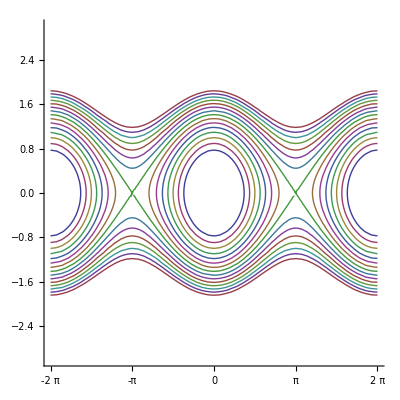

```mathematica
ContourPlot[{θdot^2-Cos[θ]==-0.4,θdot^2-Cos[θ]==-0.2,θdot^2-Cos[θ]==0,θdot^2-Cos[θ]==0.2,θdot^2-Cos[θ]==0.4,θdot^2-Cos[θ]==0.6000000000000001,θdot^2-Cos[θ]==0.8,θdot^2-Cos[θ]==1.,θdot^2-Cos[θ]==1.2000000000000002,θdot^2-Cos[θ]==1.4000000000000001,θdot^2-Cos[θ]==1.6,θdot^2-Cos[θ]==1.8,θdot^2-Cos[θ]==2.,θdot^2-Cos[θ]==2.2,θdot^2-Cos[θ]==2.4000000000000004},{θ,-2π,2π},{θdot,-3,3},Frame->False,Axes->True,Ticks->{{-2π,-π,0,π,2π},{}}]
```